## An Implementation of Quantitative Realism

## Data Structures

### Parameters

#### Get and Set

Global variables can be called by other functions without having them passed in as arguments. This function provides a way to set global parameters from an Association. Output: none.

```mathematica
SetParameters[p_Association]:= Block[{},
β=N[Lookup[p,"β",β]]; (* Constructive power multiplier *)
μ=N[Lookup[p,"μ",μ]]; (* Destructive power multiplier *)
λ=N[Lookup[p,"λ",λ]]; (* Rate of power decay *)
α=N[Lookup[p,"α",α]]; (* Utility function exponent *)
δ=N[Lookup[p,"δ",δ]]; (* Discount rate *)
ρ=N[Lookup[p,"ρ",ρ]]; (* Minimum self-allocation percentage *)
k=Lookup[p,"k",k]; (* Steps used in PrinceRank simulations *)
Δ=Lookup[p,"Δ",Δ]; (* Minimax pruning delta *)
discountFactors=(1-δ)*Table[δ^i,{i,k}];
]
```

Set the global parameters. Output: none.

```mathematica
SetParameters[<|"β"->2,"μ"->5,"λ"->.995,"α"->2.25,"δ"->0.8, "ρ"->0.98,"k"->9,"Δ"->0.2|>]
```

Assembles global parameters into an Association. Output: Association.

```mathematica
GetParameters:= <|"β"-> β,"μ"-> μ,"λ"-> λ,"α"-> α,"δ"-> δ,"ρ"-> ρ,"k"->k,"Δ"->Δ|>
```

Generate a string showing the parameters. Output: string.

```mathematica
ParameterString:=Caption[
"β="<>ToString[β]<>", μ="<>ToString[μ]<>", λ="<>ToString[λ]<>", α="<>ToString[α]<>", ρ="<>ToString[ρ]<>", δ="<>ToString[δ](*<>, "k="<>ToString[k]<>", Δ="<>ToString[Δ]*)];
```

#### n

Determine the number of agents in a power structure. Output: integer.

This is slow. Maybe delete?

```mathematica
Clear[n];
n[ps_Association]:=Length[ps["s"]];
n[T_List]:=Length[T];
```

#### Discount rate (δ)

Discount rate error threshold (5%).

```mathematica
discountErrorThreshold = 0.05;
```

Given the discount rate δ, returns the number of future steps required. Output: integer.

```mathematica
DeltaToSteps[δ_Real]:=DeltaToSteps[δ]=Ceiling[Log[δ,discountErrorThreshold]]
```

```mathematica
DeltaToSteps[δ_Real]:=Ceiling[Log[δ,discountErrorThreshold]]
```

Given a number of steps, returns the value of δ that would require those steps. Output: real number.

```mathematica
StepsToDelta[steps_Integer]:= Surd[discountErrorThreshold,steps]
```

### Power Structures

#### PowerStructure

A power structure is represented as an Association composed of a size vector (s) and a tactic matrix (T). The following functions instantiate power structures. They should be avoided when performance matters.

```mathematica
<|"s"->{4.3,4.2},"T"->{{0.5,0.5},{-0.5,0.5}}|>
```

Creates a new power structure object. If the tactic matrix is ternary, it gets legalized. Output: power structure.

```mathematica
PowerStructure[s_List,T_List?TernaryMatrixQ]:= PowerStructure[s,NormalizeTernaryT[T]]
```

Creates a new power structure object. This is the base function. Output: power structure.

```mathematica
PowerStructure[s_List,T_List?MatrixQ]:= <|"s"->N[s],"T"->N[T]|>
```

Creates a new power structure from only a tactic matrix. If the tactic matrix is ternary, it gets legalized. The size vector is a list of 1s. Output: power structure.

```mathematica
PowerStructure[T_List?TernaryMatrixQ]:= PowerStructure[NormalizeTernaryT[T]]
```

Same as the above, but it does not alter the tactic matrix.

```mathematica
PowerStructure[T_List?MatrixQ]:= PowerStructure[Table[1.,Length[T]],T]
```

#### RandomPowerStructure

Generate a random power structure, specifying the number of nodes (n). By convention, the size vector in the first state of a simulation is normalized. Output: power structure.

```mathematica
RandomPowerStructure[n_Integer]:= PowerStructure[RandomS[n],RandomT[n]]
```

#### RandomS

Creates a random size vector for n agents, normalized to unity. Output: size vector.

```mathematica
RandomS[n_Integer]:= NormalizeS[RandomReal[{0,1},n]]
```

Unit tests:

```mathematica
unitTests["RandomS"] :={
VerificationTest[
Max[RandomS[5]],
1.,
TestID->"RandomS1"
]
};
```

#### RandomTernaryPowerStructure

Generate a random power structure, of size n, with symmetric ternary edges and small-world connectivity. Output: power structure.

```mathematica
RandomTernaryPowerStructure[n_Integer]:=RandomTernaryPowerStructure[n,2n,0.1]
```

```mathematica
RandomTernaryPowerStructure[n_Integer,edges_Integer,negativity_Real]:=PowerStructure[RandomS[n],NormalizeTernaryT[RandomTernaryT[n,edges,negativity]]]
```

#### Pretty

Displays a power structure with rounded values and components shown in MatrixForm. Output: a power structure.

```mathematica
Pretty[ps_Association]:= Map[MatrixForm[PrettyRound[#,.001]]&,ps]
PrettyRound[x_,n_]:=DeDecimalize[Round[x,n]];
PrettyRound[x_List?TernaryMatrixQ,n_]:=DeDecimalize[x];
```

```mathematica
Pretty[RandomPowerStructure[3]]
```

<|s→(0.581
0.493
1.),T→(0.906 | -0.029 | -0.021
-0.073 | 0.959 | -0.029
0.021 | 0.013 | 0.95)|>

A version that can be called on a tactic matrix. Output: a tactic matrix.

```mathematica
Pretty[T_List?MatrixQ]:=MatrixForm[PrettyRound[T,.001]]
```

## Helper Functions

### Scalar

#### DeDecimalize

Removes extraneous decimal points from integers. Output: number.

```mathematica
DeDecimalize[n_]:=If[n==IntegerPart[n],IntegerPart[n],n]
```

### List

#### PositionLargest

Gives the position of the first element that has the largest value in list. Stolen from: https://resources.wolframcloud.com/FunctionRepository/resources/PositionLargest.  Output: list of integers.

```mathematica
PositionLargest[list_List]/;AllTrue[list,NumericQ]:=First[FirstPosition[list,Max[list]]]
```

```mathematica
PositionLargest[list_List,n_Integer]/;AllTrue[list,NumericQ]:=Take[Flatten[Position[list,#]&/@DeleteDuplicates[TakeLargest[list,n]]],n]
```

```mathematica
PositionLargest[list_List,HoldPattern[UpTo][n_Integer]]/;AllTrue[list,NumericQ]:=Take[Flatten[Position[list,#]&/@DeleteDuplicates[TakeLargest[list,UpTo[n]]]],UpTo[n]]
```

#### RandomPosition

Gives a random position at which objects matching pattern appear in expr.

```mathematica
RandomPosition[expr_,pattern_]:= RandomChoice[Flatten[Position[expr,pattern]]]
```

```mathematica
RandomPosition[{a,a,b,a,c,b},b]
```

5

### Matrix

#### MapTransposed

Maps a function down the columns of a matrix. Output: matrix.

```mathematica
MapTransposed[f_,M_List?MatrixQ]:= Transpose[Map[f,Transpose[M]]];
SetAttributes[MapTransposed,HoldFirst];
```

#### ReplaceColumn

Replace a column in a matrix M with a given list. Output: matrix.

```mathematica
ReplaceColumn[M_List,i_Integer,list_List]:=Block[{m=M},
m[[All,i]]=list;
Return[m];
]
```

#### ReplaceDiagonal

Replaces the diagonal of a matrix with a given list.  This implementation is ugly but fast. Output: matrix. NOTE: This is not used anywhere.

```mathematica
ReplaceDiagonal[M_List?MatrixQ,diag_List] := M - DiagonalMatrix[Diagonal[M]] + DiagonalMatrix[diag]
```

A faster version to use when all input elements are known to be reals.

```mathematica
ReplaceDiagonalReals=FunctionCompile[Function[{
Typed[M,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[diag,TypeSpecifier["PackedArray"]["Real64",1]]
},Block[{R=M,i,m=Length[M]},
For[i=1,i≤m,i++,  
R[[i,i]] = diag[[i]];
]; 
Return[R];
]]];
```

#### ZeroDiagonalize

Overwrites the diagonal of a matrix with all zeroes. Every element in the matrix is assumed to be a Real. Output: a matrix.

```mathematica
ZeroDiagonalize[M_List]:=ReplaceDiagonalReals[M,Table[0.,Length[M]]]
```

#### ZeroMatrix

Creates a matrix of all zeroes, of a given dimension. Output: matrix.

```mathematica
ZeroMatrix[n_]:=Table[0,{i,n},{j,n}]
```

```mathematica
ZeroMatrix[4]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Unit tests

Unit tests for the helper functions:

```mathematica
unitTests["HelperFunctions"]:={
VerificationTest[
MapTransposed[Differences,IdentityMatrix[4]],
{{-1,1,0,0},{0,-1,1,0},{0,0,-1,1}},
TestID->"HelperFunctions_MapTransposed1"
],
VerificationTest[
ReplaceColumn[IdentityMatrix[3],1,{5,6,7}],
{{5,0,0},{6,1,0},{7,0,1}},
TestID->"HelperFunctions_ReplaceColumn1"
],
VerificationTest[
ReplaceDiagonalReals[N[IdentityMatrix[3]],N[{9,10,11}]],
N[{{9,0,0},{0,10,0},{0,0,11}}],
TestID->"HelperFunctions_ReplaceDiagonal1"
],
VerificationTest[
PositionLargest[{100,200,100,200,50}],
2,
TestID->"HelperFunctions_PositionLargest1"
],
VerificationTest[
PositionLargest[{100,200,100,200,50},1],
{2},
TestID->"HelperFunctions_PositionLargest2"
],
VerificationTest[
PositionLargest[{100,200,100,200,50},3],
{2,4,1},
TestID->"HelperFunctions_PositionLargest3"
],
VerificationTest[
ZeroDiagonalize[N[{{2,6,8},{5,9,6},{6,6,2}}]],
N[{{0,6,8},{5,0,6},{6,6,0}}],
TestID->"HelperFunctions_ZeroDiagonalize1"
]
};
```

## Tactics

### Type testing

#### LegalTacticQ

Determines whether a tactic vector is legal, in the sense that the total of the absolute values of all tactics is 1. Output: Boolean.

```mathematica
LegalTacticQ[tactic_List] := Total[Abs[tactic]]==1;
```

Unit tests:

```mathematica
unitTests["LegalTacticQ"] :={
VerificationTest[
LegalTacticQ[{.5,0,0,-.5}],
True,
TestID->"LegalTacticQ1"
],
VerificationTest[
LegalTacticQ[{.5,.2,0,-.5}],
False,
TestID->"LegalTacticQ2"
]
};
```

#### LegalTQ

Determines whether a tactic matrix is legal (see above). Output: Boolean.

```mathematica
LegalTQ[T_List?MatrixQ]:= AllTrue[Map[LegalTacticQ,Transpose[T]],TrueQ];
```

Unit tests:

```mathematica
unitTests["LegalTQ"] :={
VerificationTest[
LegalTQ[({{0.5, 0.3}, {-0.5, 0.7}})],
True,
TestID->"LegalTQ1"
],
VerificationTest[
LegalTQ[({{0.6, 0.3}, {-0.5, 0.7}})],
False,
TestID->"LegalTQ2"
]
};
```

#### TernaryMatrixQ

Determines whether a matrix is a ternary matrix (i.e. one composed only of -1, 0, or 1s). Output: Boolean.

```mathematica
TernaryMatrixQ[T_List?MatrixQ]:= ContainsOnly[Flatten[T],{-1.,0.,1.}]
```

Unit tests:

```mathematica
unitTests["TernaryMatrixQ"] :={
VerificationTest[
TernaryMatrixQ[N[IdentityMatrix[3]]],
True,
TestID->"TernaryMatrixQ1"
],
VerificationTest[
TernaryMatrixQ[RandomReal[{0,1},{3,3}]],
False,
TestID->"TernaryMatrixQ2"
]
};
```

### Normalization

#### NormalizeS

Normalizes the size vector so that all sizes are between 0 and 1.  The largest agent always ends up with a size of 1. This is slightly faster than an equivalent complied version. Output: size vector.

```mathematica
NormalizeS[s_List] := Block[{max=Max[s]},
N[If[max==0,s,s/max]]
]
```

A version that works on power structures. Output: power structure.

```mathematica
NormalizeS[ps_Association]:= <|"s"->NormalizeS[ps["s"]],"T"->ps["T"],"pr"->Lookup[ps,"pr",{}],"i"->Lookup[ps,"i",{}]|>
```

Unit tests:

```mathematica
unitTests["NormalizeS"] :={
VerificationTest[
NormalizeS[{0,0,0}],
{0.,0.,0.},
TestID->"NormalizeS1"
],
VerificationTest[
NormalizeS[{.5,.3,0}],
{1.,0.6,0.},
TestID->"NormalizeS2"
],
VerificationTest[
NormalizeS[{5,13,0.3}],
{0.38461538461538464,1.,0.023076923076923078},
TestID->"NormalizeS3"
]
};
```

#### NormalizeTactic

Given a random tactic vector, this function adjusts its length so as to make it a legal tactic.  A legal tactic is a point on the surface of a cross-polytope whose dimension is equal to the number of agents. Note: A zero vector 0 will remain 0. Output: tactic vector.

```mathematica
NormalizeTactic[list_List]:=NormalizeTacticCompiled[N[list]]
```

```mathematica
NormalizeTacticCompiled=FunctionCompile[Function[{
Typed[list,TypeSpecifier["PackedArray"]["Real64",1]]
},If[Total[Abs[list]]==0,list,list / Total[Abs[list]]]]];
```

Unit tests:

```mathematica
unitTests["NormalizeTactic"] :={
VerificationTest[
NormalizeTactic[{0.1,0,0}],
{1.,0.,0.},
TestID->"NormalizeTactic1"
],
VerificationTest[
NormalizeTactic[{0,0,0}],
{0.,0.,0.},
TestID->"NormalizeTactic2"
],
VerificationTest[
NormalizeTactic[{1,2,4,4.}],
{0.09090909090909091,0.18181818181818182,0.36363636363636365,0.36363636363636365},
TestID->"NormalizeTactic3"
],
VerificationTest[
NormalizeTactic[{-1,0,0,1}],
{-0.5,0.,0.,0.5},
TestID->"NormalizeTactic2"
]
};
```

#### NormalizeT

Output: a normalized tactic matrix.

```mathematica
NormalizeT[T_List?MatrixQ]:=MapTransposed[NormalizeTactic,T]
```

#### NormalizeTernaryT

Legalizes a ternary matrix, which is a different algorithm because ρ has to be inserted for the self-allocations. Note: the self-allocation will always be ρ, even if all other allocations are 0. Output: tactic matrix.

```mathematica
NormalizeTernaryT[T_List] :=ReplaceDiagonalReals[Transpose[Transpose[T]/ReplaceAll[N[Total[Abs[T]]], 0.->1.]]*(1.-ρ),Table[ρ,Length[T]]]
```

A version that sets ρ to 1 when all other allocations are 0:

```mathematica
NormalizeTernaryT[T_List] :=Block[{x,t=N[Total[Abs[T]]]},
x=Transpose[Transpose[T]/ReplaceAll[t, 0.->1.]]*(1.-ρ);
ReplaceDiagonalReals[x,Map[If[#==0.,1.,ρ]&,t]]
]
```

Unit tests:

```mathematica
unitTests["NormalizeTernaryT"] :={
VerificationTest[
NormalizeTernaryT[{{0,1},{-1,0}}],
{{0.9,0.09999999999999998},{-0.09999999999999998,0.9}},
TestID->"NormalizeTernaryT1"
]
};
```

#### NormalizeTernaryTactic

Given a ternary tactic vector, convert it to a legal tactic vector. The focal agent gets a preset self-allocation, and all of the outgoing allocations are apportioned accordingly. Self-allocations on the input tactic are ignored. Output: tactic vector.

```mathematica
NormalizeTernaryTactic[tactic_List,i_Integer]:= ReplacePart[NormalizeTacticCompiled[tactic] * (1.-ρ),i->ρ]
```

```mathematica
RepeatedTiming[NormalizeTernaryTactic[{1.,1.,0.,-1.,0.},5],5]
```

{5.5×10^-6,{0.0333333,0.0333333,0.,-0.0333333,0.9}}

```mathematica
NormalizeTernaryTactic[{0.,0.,0.},5]
```

{0.,0.,0.}

#### InsertSelfAllocation

Given a tactic vector, set the self-allocation percentage ρ of agent i such that the result is a legal tactic vector. It is assumed that the self-allocation amount in the input tactic vector is 0. Output: tactic vector.

```mathematica
InsertSelfAllocation[tactic_,i_]:= ReplacePart[tactic,i->1-Total[Abs[tactic]]]
```

```mathematica
InsertSelfAllocation[{0,0.035,0,-0.009,0},1]
```

{0.956,0.035,0,-0.009,0}

#### GravitizeTernaryT

Given a ternary tactic matrix, adjust the allocations to make them proportional to the sizes of the agents. The resulting allocations will be akin to a gravity model of trade. Output: tactic matrix.

```mathematica
GravitizeTernaryT[T_,s_]:=NormalizeTernaryT[s*T]
```

```mathematica
GetParameters[]
```

<|β→2.,μ→5.,λ→0.995,α→2.25,δ→0.8,ρ→0.985,k→9,Δ→0.05|>

```mathematica
SetParameters[<|"β"->2.,"μ"->5.,"λ"->0.995,"α"->2.25,"δ"->0.8,"ρ"->0.9,"k"->9,"Δ"->0.05|>];s={.8,1,.2,.3,.6,.3};
T=RandomTernaryT[6,3,.3];
{T//MatrixForm,GravitizeTernaryT[T,s]//MatrixForm}
```

{(0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 0.),(0.9 | 0. | 0. | 0. | 0.0727273 | 0.
0. | 0.9 | 0.1 | 0. | 0. | 0.
0. | 0.1 | 0.9 | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
0.1 | 0. | 0. | 0. | 0.9 | 0.1
0. | 0. | 0. | 0. | 0.0272727 | 0.9)}

```mathematica
ShowPowerStructure[PowerStructure[s,GravitizeTernaryT[T,s]],<|"ternary"->False|>]
```

-Graphics-

A second form of gravitization gives each relationship a fixed amount of potential power that’s proportional to the other agents’ sizes. The tactic vector is then normalized by allocating all unused power back to each agent. Output: tactic vector.

```mathematica
GravitizeTernaryTactic[tactic_,s_,i_]:=InsertSelfAllocation[tactic*s*(1-ρ)/Total[s],i]
```

Applies the second form of gravitization to a tactic matrix. Output: tactic matrix.

```mathematica
GravitizeTernaryT[T_,s_]:=Transpose[MapIndexed[GravitizeTernaryTactic[#,s,First[#2]]&,Transpose[T]]]
```

```mathematica
s={.8,1,.2,.3,.6,.3};
T=RandomTernaryT[6,3,.3];
{T//MatrixForm,GravitizeTernaryT[T,s]//MatrixForm}
```

{(0. | 1. | 0. | 0. | 0. | 1.
1. | 0. | 1. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0.),(0.959375 | 0.025 | 0. | 0. | 0. | 0.025
0.03125 | 0.96875 | 0.03125 | 0. | 0. | 0.
0. | 0.00625 | 0.96875 | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0.009375 | 0. | 0. | 0. | 0. | 0.975)}

### Continuous Tactics

#### RandomTactic

Generates a random tactic vector. Note that this may entail self-harm. Output: tactic vector.

```mathematica
RandomTactic[n_Integer]:=NormalizeTactic[RandomPoint[Sphere[Table[0,n]]]]
```

Generates a random tactic vector in which a specified agent is not harming itself. The allocation to the focal agent is at least ρ. Output: tactic vector.

```mathematica
RandomTactic[n_Integer,index_Integer]:=With[{a=RandomReal[{ρ,1}]},
Insert[(1-a)RandomTactic[n-1],a,index]
]
```

Unit tests:

```mathematica
unitTests["RandomTactic"] :={
VerificationTest[
LegalTacticQ[RandomTactic[5]],
True,
TestID->"RandomTacticVector1"
],
VerificationTest[
First[RandomTactic[5,1]]>0,
True,
TestID->"RandomTacticVector2"
]
};
```

#### RandomT

Generates a random tactic matrix for n agents. Output: tactic matrix.

```mathematica
RandomT[n_Integer] :=Transpose[Table[RandomTactic[n,i],{i,n}]]
```

Unit tests:

```mathematica
unitTests["RandomTacticMatrix"] :={
VerificationTest[
LegalTQ[RandomT[3]],
True,
TestID->"RandomTacticMatrix1"
]
};
```

#### RandomTNear

Given a tactic matrix, randomly alter agent i’s tactic with respect to another randomly selected agent j. The resulting tactic is symmetrical (reciprocal) in the sense that T_ijand T_jihave the same polarity, even if they vary in intensity. Only one relationship is altered. Output: tactic matrix.

```mathematica
RandomTNear[T_,i_]:=Block[{j,ti,tj},
j=RandomChoice[Delete[Range[Length[T]],i]]; 
{ti,tj}=RandomReal[{0,RandomChoice[{1,-1}]*(1.-ρ)},2];
ReplaceColumn[ReplaceColumn[T,i,NormalizeTernaryTactic[ReplacePart[T[[All,i]],{j->tj,i->0.}],i]],j,NormalizeTernaryTactic[ReplacePart[T[[All,j]],{i->ti,j->0.}],j]]
]
```

#### RandomTacticNear

Given a tactic vector, this function finds another tactic (approximately) within a given Euclidean distance σ. It is assumed that agents do not harm themselves. The new tactic is found by: (1) starting from a point represented by the original tactic, (2) picking a random point on a sphere of radius σ, centered at the original point, (3) ensuring that the self-allocation is nonnegative, and (4) normalizing the point on the sphere back to the surface of the n-dimensional cross-polytope. Output: tactic vector.

```mathematica
RandomTacticNear[tactic_List, index_Integer, σ_Real] := NormalizeTactic[MapAt[Abs,RandomPoint[Sphere[tactic,σ]],index]]
```

### Ternary Tactics

#### MovesNear

Given a power structure, find nearby ternary moves (not necessarily symmetric) which apply the law of motion. Nearness is assumed to be dx=1. Output: list of power structures.

```mathematica
MovesNear[ps_Association,i_Integer]:=Block[{s=ps["s"],T=ps["T"]},
Map[UpdatePowerStructure[PowerStructure[s,NormalizeTernaryT[#]]]&,TernaryTsNear[ToTernary[T],i,1]]]
```

```mathematica
ps=PowerStructure[{1.,1.,1.},Symmetric3s[[21]]];
MovesNear[ps,1]
```

{<|s→{0.85,0.85,0.85},T→{{0.9,0.05,-0.05},{-0.05,0.9,0.05},{-0.05,0.05,0.9}}|>,<|s→{0.85,1.,0.7},T→{{0.9,0.05,-0.05},{0.,0.9,0.05},{-0.1,0.05,0.9}}|>,<|s→{0.85,1.1,0.85},T→{{0.9,0.05,-0.05},{0.05,0.9,0.05},{-0.05,0.05,0.9}}|>,<|s→{0.85,1.2,1.},T→{{0.9,0.05,-0.05},{0.1,0.9,0.05},{0.,0.05,0.9}}|>,<|s→{0.85,1.1,1.1},T→{{0.9,0.05,-0.05},{0.05,0.9,0.05},{0.05,0.05,0.9}}|>}

#### RandomTernaryT

Generate a random symmetric ternary tactic matrix of size n, with a given number of edges, some percentage of which are negative. This function piggybacks on RandomGraph to generate a small-world graph with a given number of nodes and edges. Output: tactic matrix.

```mathematica
RandomTernaryT[n_Integer]:=RandomTernaryT[n,2n,0.1]
```

```mathematica
RandomTernaryT[n_Integer,edges_Integer,negativity_Real]:=Block[{T,g=RandomGraph[{n,edges}]},
T=Normal[SparseArray[Map[#[[1]]-> RandomChoice[{negativity,1-negativity}-> {-1.,1.}]&,Drop[ArrayRules[UpperTriangularize[AdjacencyMatrix[g]]],-1]],{n,n}]];
N[T+Transpose[T]]
]
```

```mathematica
RandomTernaryT[8,10,0.1] //Pretty
```

(0 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0)

#### Symmetric3s

There are 729 legal tactic matrices for n=3. Of these, 27 are symmetric.

```mathematica
Legal3s:=DeleteDuplicates[Map[N[ZeroDiagonalize[#]]&,Tuples[{-1.,0.,1.},{3,3}]]];
Symmetric3s = Select[Legal3s,SymmetricMatrixQ];
```

```mathematica
RandomChoice[Symmetric3s]//MatrixForm
```

(0. | -1. | -1.
-1. | 0. | 1.
-1. | 1. | 0.)

#### SymmetricMovesNear

Given a power structure, find nearby symmetric ternary moves which apply the law of motion. Nearness is assumed to be dx=1. Output: list of power structures.

```mathematica
SymmetricMovesNear[ps_Association,i_Integer]:=Map[Join[#,<|"pr"->PrinceRank[#]|>]&,Map[<|"s"-> UpdateS[ps["s"],#],"T"-> #|>&,SymmetricTsNear[ps["T"],i]]]
```

#### SymmetricTsNear

Given a normalized tactic matrix and a focal agent i whose tactic vector we want to permute, generate all possible symmetric tactic matrices at a distance of one changed ternary tactic. Output: list of normalized tactic matrices

```mathematica
SymmetricTsNear[T_List,i_Integer]:=With[{TT=ToTernary[T]},
Join[{T},Map[NormalizeTernaryT[ReplacePart[TT,#]]&,Flatten[Delete[Table[
If[TT[[i,j]]≠t,{{i,j}->t,{j,i}->t},Nothing]
,{j,Length[T]},{t,-1.,1.}],i],1]]]
]
```

```mathematica
MatrixForm/@SymmetricTsNear[NormalizeTernaryT[ZeroMatrix[3]],3]
```

{(0.9 | 0. | 0.
0. | 0.9 | 0.
0. | 0. | 0.9),(0.9 | 0. | -0.1
0. | 0.9 | 0.
-0.1 | 0. | 0.9),(0.9 | 0. | 0.1
0. | 0.9 | 0.
0.1 | 0. | 0.9),(0.9 | 0. | 0.
0. | 0.9 | -0.1
0. | -0.1 | 0.9),(0.9 | 0. | 0.
0. | 0.9 | 0.1
0. | 0.1 | 0.9)}

Given a ternary tactic matrix and a focal agent i whose tactic vector we want to permute, generate all possible symmetric tactic matrices within a given (Hamming) distance. Output: list of ternary tactic matrices.

```mathematica
SymmetricTsNear[T_List,i_Integer,dx_Integer]:=Map[ReplacePart[ReplaceColumn[T,i,#],i->#]&,TernaryTacticsNear[T,i,dx]]
```

Same as the above, but assumes that dx=1. Output: list of ternary tactic matrices.

```mathematica
SymmetricTsNear[T_List,i_Integer]:=Map[ReplacePart[ReplaceColumn[T,i,#],i->#]&,TernaryTacticsNear[T[[All,i]],i]]
```

A version that returns random continuous tactics. Not an efficient implementation, as ideally I would restructure how Minimax explores moves, but good enough for determining whether continuous tactics are viable. Output: list of tactic matrices.

```mathematica
SymmetricTsNear[T_List,i_Integer]:=Join[{T},Table[RandomTNear[T,i],20]]
```

#### SymmetrizePowerStructure

Given a power structure, convert it the tactic matrix to ternary, symmetrize it, and convert it back to a power structure. Output: power structure.

```mathematica
SymmetrizePowerStructure[ps_Association]:=PowerStructure[ps["s"],NormalizeTernaryT[SymmetrizeT[ToTernary[ps["T"]]]]]
```

#### SymmetrizeT

Given an asymmetric ternary tactic matrix that reflects each agents’ desired move, find T where the applicable relationship is the minimum of each set of pairwise moves.

Rename: SymmetrizeTernaryT?

```mathematica
SymmetrizeT[T_List]:=MapThread[Min,{T,Transpose[T]},2]
```

```mathematica
SymmetrizeT[({{0, 1, 0, -1}, {1, 0, 0, 1}, {1, 0, 0, 0}, {0, -1, 0, 0}})] // MatrixForm
```

(0 | 1 | 0 | -1
1 | 0 | 0 | -1
0 | 0 | 0 | 0
-1 | -1 | 0 | 0)

#### TernaryTacticsNear

Given a ternary tactic matrix and an agent index i, list all possible tactic vectors in which a single move is altered, within a given Hamming distance. This function will also return the original tactic. Output: a list of tactic vectors.

```mathematica
TernaryTacticsNear[T_List,i_Integer,dx_Integer]:=DeleteDuplicates[Flatten[Map[Tuples[ReplacePart[Partition[T[[All,i]],1],Map[#->{-1.,0.,1.}&,#]]]&,Subsets[Delete[Range[Length[T]],i],{dx}]],1]]
```

A variant for when dx=1.

```mathematica
TernaryTacticsNear[tactic_List,i_Integer]:=DeleteDuplicates[Flatten[
Table[If[j==i,Nothing,{ReplacePart[tactic,j-> -1.],ReplacePart[tactic,j-> 0.],ReplacePart[tactic,j-> 1.]}],{j,Length[tactic]}],1]]
```

```mathematica
TernaryTacticsNear[{1.,1.,1.},3]
```

{{-1.,1.,1.},{0.,1.,1.},{1.,1.,1.},{1.,-1.,1.},{1.,0.,1.}}

#### TernaryTsNear

Given a ternary tactic matrix and a focal agent i whose tactic vector we want to permute, generate all possible tactic matrices (not necessarily symmetric) within a given (Hamming) distance. Output: list of ternary tactic matrices.

```mathematica
TernaryTsNear[T_List,i_Integer,dx_Integer]:=Map[ReplaceColumn[T,i,#]&,TernaryTacticsNear[T,i,dx]]
```

```mathematica
MatrixForm/@TernaryTsNear[N[IdentityMatrix[3]],2,1]
```

{(1. | -1. | 0.
0. | 1. | 0.
0. | 0. | 1.),(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.),(1. | 1. | 0.
0. | 1. | 0.
0. | 0. | 1.),(1. | 0. | 0.
0. | 1. | 0.
0. | -1. | 1.),(1. | 0. | 0.
0. | 1. | 0.
0. | 1. | 1.)}

#### ToTernary

Converts a legal tactic matrix to a ternary one. Output: tactic matrix.

```mathematica
ToTernary[T_List]:=ReplaceDiagonalReals[N[Sign[T]],Table[0.,Length[T]]]
```

Convert the tactic matrix within a power structure to ternary. Output: power structure.

```mathematica
ToTernary[ps_Association]:= <|"s"->ps["s"],"T"-> ToTernary[ps["T"]]|>
```

Unit tests:

```mathematica
unitTests["ToTernary"] :={
VerificationTest[
ToTernary[{{0.47593052648072004,0.38946778511397906,0.5887854695349517},{0.36321528609957204,0.1477143527714231,-0.3520164533294082},{0.16085418741970775,0.4628178621145978,0.05919807713564013}}],
{{0.,1.,1.},{1.,0.,-1.},{1.,1.,0.}},
TestID->"ToTernary1"
]
};
```

#### Focal Agent Symmetric Triads

Generate a symmetrical tactic matrix from a tuple of {-1, 0, 1}’s.

```mathematica
GenerateSymmetricTernaryTacticMatrix[{a_,b_,c_}]:=({{0, a, c}, {a, 0, b}, {c, b, 0}})
```

Remove tuples that are symmetrical from agent #1’s perspective.

```mathematica
FocalAgentSymmetricTriads = Map[GenerateSymmetricTernaryTacticMatrix,{{-1,-1,-1},{-1,-1,0},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,1,-1},{-1,1,0},{-1,1,1},{0,-1,0},{1,-1,0},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,-1,-1},{1,-1,1},{1,0,1},{1,1,1}}];
```

### Get and Set Tactics

#### GetTactic

Gets an agent’s tactic vector from a power structure. Output: tactic vector.

```mathematica
GetTactic[ps_Association,i_Integer]:= ps["T"][[All,i]]
```

```mathematica
GetTactic[T_List,i_Integer]:=T[[All,i]]
```

#### SetTactic

Replaces an agent’s tactic in a matrix with a new tactic vector. Output: tactic matrix.

```mathematica
SetTactic[T_List,tactic_List,i_Integer]:= ReplaceColumn[T,i,tactic]
```

Replaces an agent’s tactic in a power structure with a new tactic vector. Output: tactic vector.

```mathematica
SetTactic[ps_Association,tactic_List,i_Integer]:= PowerStructure[ps["s"],ReplaceColumn[ps["T"],i,tactic]]
```

Unit tests:

```mathematica
unitTests["SetTactic"]:={
VerificationTest[
SetTactic[IdentityMatrix[3],{4,5,6},2],
{{1,4,0},{0,5,0},{0,6,1}},
TestID->"SetTactic1"
]
};
```

### Defection

#### DefectionQ

Used in the last round of a game tree to determine whether player i’s move ps2, from initial state ps1, is considered a defection with respect to any of the other players. A defection occurs when the value of the moving player’s tactic is less than the minimum of the two current tactics of the pair of players. The idea is that on the last move, a player is prevented from lowering its tactic in a way that undercuts reciprocity, since the other player will not have a chance to retaliate. Output: Boolean.

```mathematica
DefectionQ[ps1_Association, ps2_Association, i_Integer]:= DefectionQ[ps1["T"], ps2["T"], i]
```

Because defection is determined in light of actual (rather than ternary) tactics, in some cases the reduction of positivity caused by a player’s increased activity with a third party is considered a defection. For example:

```mathematica
DefectionQ[PowerStructure[{1,1,1},({{0, 1, 1}, {1, 0, 0}, {0, 0, 0}})],PowerStructure[{1,1,1},({{0, 1, 1}, {1, 0, 0}, {1, 0, 0}})],1]
```

True

This version of the function takes tactic matrices (either ternary or continuous) instead of power structures. Output: Boolean.

```mathematica
DefectionQ[T1_List, T2_List, i_Integer]:=AnyTrue[Delete[Table[T2[[j,i]]<Min[T1[[j,i]],T1[[i,j]]],{j,n[T1]}],i],TrueQ]
```

If ternary matrices are used with this version of the function, it avoids the case illustrated above:

```mathematica
DefectionQ[({{0, 1, 1}, {1, 0, 0}, {0, 0, 0}}),({{0, 1, 1}, {1, 0, 0}, {1, 0, 0}}),1]
```

False

### Named Ts

#### NamedTHierarchy

A tactic matrix of variable size representing a hierarchy. Output: tactic matrix.

```mathematica
NamedTHierarchy[n_]:=NormalizeTernaryT[ReplacePart[ReplaceColumn[ReplacePart[ZeroMatrix[n],1-> Table[1.,n]],1,Table[1.,n]],{1,1}->0.]]
```

```mathematica
NamedTHierarchy[5]//MatrixForm
```

(0.98 | 0.02 | 0.02 | 0.02 | 0.02
0.005 | 0.98 | 0. | 0. | 0.
0.005 | 0. | 0.98 | 0. | 0.
0.005 | 0. | 0. | 0.98 | 0.
0.005 | 0. | 0. | 0. | 0.98)

#### NamedTComplete

A tactic matrix of variable size representing a fully connected graph. Output: tactic matrix.

```mathematica
NamedTComplete[n_]:=NormalizeTernaryT[ReplaceDiagonalReals[Table[1.,{i,n},{j,n}],Table[0.,n]]]
```

```mathematica
NamedTComplete[4]//MatrixForm
```

(0.98 | 0.00666667 | 0.00666667 | 0.00666667
0.00666667 | 0.98 | 0.00666667 | 0.00666667
0.00666667 | 0.00666667 | 0.98 | 0.00666667
0.00666667 | 0.00666667 | 0.00666667 | 0.98)

#### NamedTNull

```mathematica
NamedTNull[n_]:=NormalizeTernaryT[ZeroMatrix[n]]
```

```mathematica
NamedTNull[4]//MatrixForm
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.)

## Simulation Engine

### Law of Motion

#### UpdateS

Update the agents’ sizes based on their current sizes and chosen tactics. The matrix T is assumed to be composed of normalized tactic vectors emitted by the agents. There can be self-allocation within T; any such values are subject to the decay constant λ. All elements in a T must be real numbers. Output: size vector.

```mathematica
UpdateS[s_,T_]:=UpdateSCompiled[s,T,β,μ,λ]
```

```mathematica
UpdateSCompiled=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[β,"Real64"],
Typed[μ,"Real64"],
Typed[λ,"Real64"]
},
Ramp[Table[If[i==j,T[[i,j]]*λ,If[T[[i,j]]<0,T[[i,j]]*μ,T[[i,j]]*β]],{i,Length[T]},{j,Length[T]}].s]
]];
```

Computes the size vector after multiple applications of the law of motion. Output: size vector.

```mathematica
UpdateS[s_List,T_List,depth_Integer]:=Fold[UpdateS[#1,#2]&,s,Table[T,depth]]
```

Same as the above, but with parameters passed in as arguments (for testing). Output: size vector.

```mathematica
UpdateS[s_List,T_List,{β_Real,μ_Real,λ_Real}]:=UpdateSCompiled[N[s],T,β,μ,λ]
```

Unit tests:

```mathematica
unitTests["UpdateS"]:={
VerificationTest[
UpdateS[{1,.4},{{0.9,-0.17},{0.1,0.83}},{2.,3.,1.}],
{0.696,0.532},
TestID->"UpdateS1"
],
VerificationTest[
UpdateS[{1.,.4},N[IdentityMatrix[2]],{2.,3.,1.}],
{1.,0.4},
TestID->"UpdateS2"
],
VerificationTest[
UpdateS[{1.,.4},N[IdentityMatrix[2]],{2.,3.,.7}],
{0.7,0.27999999999999997},
TestID->"UpdateS3"
],
VerificationTest[
UpdateS[Range[10],N[IdentityMatrix[10]],{1.2,2.,.98}] ,
{0.98,1.96,2.94,3.92,4.9,5.88,6.86,7.84,8.82,9.8},
TestID->"UpdateS4"
],
VerificationTest[
UpdateS[{1,1,1},N[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})],{1.2,3.,1.}],
{1.,1.,1.}, 
TestID->"UpdateS5"
],
VerificationTest[
UpdateS[{0,0,0},N[({{0, 1, 0}, {1, 0, 1}, {0, 0, 0}})],{2.,3.,1.}],
{0.,0.,0.},
TestID->"UpdateS6"
],
VerificationTest[
UpdateS[{1,1,1},N[({{0, 1, 0}, {1, 0, -1}, {0, 0, 0}})],{2.,3.,1.}],
{2.,0.,0.},
TestID->"UpdateS7"
],
VerificationTest[
UpdateS[{1.,1.,1.},N[({{.9, 0, 0}, {.1, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{0.9,1.2,1.},
TestID->"UpdateS8"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, 0, 0}, {-.1, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{0.9,0.7,1.},
TestID->"UpdateS9"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.5, 0, 0}, {-.5, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{0.5,0.,1.},
TestID->"UpdateS10"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.5, 0, 0}, {-.5, 1, 0}, {0, 0, 1}})],{2.,3.,.9}],
{0.45,0.,0.9},
TestID->"UpdateS11"
] ,
VerificationTest[
UpdateS[{1,1,1},N[({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})],{1.2,2.,1.}],
{0.,0.,0.},
TestID->"UpdateS12"
],
VerificationTest[
UpdateS[{1,1,1},N[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})],{2.,3.,1.}],
{1.,1.,1.},
TestID->"UpdateS13"
],
VerificationTest[
UpdateS[{1,1,1},N[({{-1, 0, 0}, {0, -1, 0}, {0, 0, -1}})],{2.,3.,1.}],
{0.,0.,0.},
TestID->"UpdateS14"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, .1, 0}, {.1, .9, 0}, {0, 0, 1}})],{2.,3.,1.}],
{1.1,1.1,1.},
TestID->"UpdateS15"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, .1, 0}, {.1, .9, 0}, {0, 0, 1}})],{2.,3.,.8}],
{0.9200000000000002,0.9200000000000002,0.8},
TestID->"UpdateS16"
],
VerificationTest[
UpdateS[{1,1,1},N[({{.9, .1, 0}, {.1, .9, -.2}, {0, 0, .8}})],{2.,3.,1.}],
{1.1,0.5,0.8},
TestID->"UpdateS17"
]
};
```

#### UpdatePowerStructure

Given a power structure and a new tactic matrix, updates the size vector and returns a new power structure. This version can be used within a Fold, which is why it takes an additional tactic matrix as input. Output: power structure.

```mathematica
UpdatePowerStructure[ps_,T_]:=<|"s"->UpdateS[ps["s"],T],"T"->T|>
```

Same as the above, but this version uses the T within the power structure in the determination of the updated size vector. Output: power structure.

```mathematica
UpdatePowerStructure[ps_]:=UpdatePowerStructure[ps,ps["T"]]
```

#### SimulateLawOfMotion

Generates a simulation (a list of power structures) by repeatedly applying the law of motion (game engine) to a power structure. None of the agents change their tactics. Output: a simulation (list of power structures).

```mathematica
SimulateLawOfMotion[ps_Association]:= SimulateLawOfMotion[ps, Table[ps["T"],DeltaToSteps[δ]]]
```

Given a sequence of tactic matrices and an initial power structure, simulate the sequence of moves and determine the resulting state at each step. Output: a simulation (list of power structures).

```mathematica
SimulateLawOfMotion[ps_Association, tacticMatrixSequence_List] := FoldList[UpdatePowerStructure[#1,#2]&,ps,tacticMatrixSequence]
```

Unit tests:

```mathematica
unitTests["SimulateLawOfMotion"]:={
VerificationTest[
LegalTQ[RandomChoice[
SimulateLawOfMotion[RandomTernaryPowerStructure[6]]
]["T"]],
True,
TestID->"SimulateLawOfMotion1"
]
};
```

### Metrics

#### Utility

This function determines the “utility” of an agent’s game position. Output: utility vector (list of n reals).

```mathematica
Utility[s_List] := UtilityCompiled[s,α]
```

```mathematica
UtilityCompiled=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[α,"Real64"]
},If[Total[s] == 0,s,s^α / Total[s^2]]]];
```

Same as the above, but takes a power structure as input. Output: utility vector (list of n reals).

```mathematica
Utility[ps_Association] := Utility[ps["s"]]
```

A simple, slow version that doesn’t handle edge cases

```mathematica
Utility[s_]:=s^α/Total[s^2]
```

Unit tests:

```mathematica
unitTests["Utility"]:={
VerificationTest[
UtilityCompiled[N[{1,2,3,3,1}],2.5],
{0.041666666666666664,0.23570226039551584,0.649519052838329,0.649519052838329,0.041666666666666664},
TestID->"Utility1"
],
VerificationTest[
UtilityCompiled[N[{0,0,0}],2.5],
{0.,0.,0.},
TestID->"Utility2"
]
};
```

#### PrinceRank

Given a power structure, returns a vector representing the PrinceRank (intertemporal utility) of each agent. PrinceRank is an evaluation of each agents’ position that assumes that agents don’t alter their tactics. Given a list of payoffs for a particular player, calculate the intertemporal utility. It is assumed that the payoff of the initial state will be omitted from this list (since intertemporal utility is based on the cumulative value of future states). This implementation is consistent with the requirement that in the first future time period (t=0 in the equation for intertemporal utility), the payoff at that time period is counted at 100% (δ^0). Output: a list of n reals.

```mathematica
PrinceRank[ps_]:=Map[#.discountFactors&,princeRankSimData[ps["s"],ps["T"],β,μ,λ,α,k]]
```

```mathematica
princeRankSimData=FunctionCompile[Function[{
Typed[s,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[T,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[β,"Real64"],
Typed[μ,"Real64"],
Typed[λ,"Real64"],
Typed[α,"Real64"],
Typed[k,"Integer64"]
},Module[{updateS,utility},
updateS=Ramp[Table[If[i==j,T[[i,j]]*λ,If[T[[i,j]]<0,T[[i,j]]*μ,T[[i,j]]*β]],{i,Length[T]},{j,Length[T]}].#]&;
utility=If[Total[#] == 0,#,#^α / Total[#^2.]]&;
Transpose[Map[utility,Rest[NestList[updateS,s,k]]]]
]]];
```

A more comprehensible version of what’s happening above:

```mathematica
PrinceRank[ps_]:=Map[#.discountFactors&,Transpose[Map[Utility,Rest[NestList[UpdateS[#,ps["T"]]&,ps["s"],k]]]]]
```

Adds a PrinceRank vector as an attribute of a power structure. Output: power structure.

```mathematica
AddPrinceRank[ps_Association]:=Join[ps,<|"pr"->PrinceRank[ps]|>]
```

A version of PrinceRank that only computes it only for agent i, for performance reasons. Approximately 10% faster than PrinceRank. Output: real number.

```mathematica
PrinceRankI[ps_,i_]:=princeRankSimData[ps["s"],ps["T"],β,μ,λ,α,k][[i]].discountFactors
```

Unit tests:

```mathematica
unitTests["PrinceRank"]:={
VerificationTest[
Length[PrinceRank[RandomTernaryPowerStructure[5]]],
5,
TestID->"PrinceRank1"
]
};
```

#### Polarity

Determines the polarity of a power structure. Polarity in international relations relates to the number of great powers in the system. For example, a unipolar system has one great power; a bipolar one has two. The definition here is more subtle: it takes into account not just the distribution of power but also the network of interrelationships in the system, effectively counting how many hubs exist. The result depends upon the parameter settings, and is not always an integer value (one can round the result if desired). Output: a real number.

```mathematica
Polarity[ps_Association]:=Total[NormalizeS[PrinceRank[ps]]^2]
```

Given a size vector, return each agent’s market share of the total power in the system. Output: list of real numbers.

```mathematica
MarketShare[s_List]:= s/Total[s]
```

Herfindahl–Hirschman Index (HHI). Output: list of reals.

```mathematica
HHI[s_]:= Total[MarketShare[s]^2]
```

A version of HHI in which market shares are normalized such that the largest entity always has a size of 1. Output: list of reals.

```mathematica
ModifiedHHI[s_]:= Total[s^2]
```

Singer concentration (1972). Output: list of reals.

```mathematica
SingerConcentration[ps_]:=Sqrt[(Total[MarketShare[ps["s"]]^2]-1/n[ps])/(1-1/n[ps])]
```

```mathematica
Concentration[ps_]:=Block[{c=SingerConcentration[ps]},
If[c≥0.4 && c≤0.5,Return["Unipolar"]];
If[c≥0.2 && c≤0.4,Return["Bipolar"]];
]
```

### Legal Moves

#### TopLegalMovesNear

Given a power structure, return the top b power structures that are legal ternary moves for agent i. The law of motion is applied. Output: list of power structures.

```mathematica
TopLegalMovesNear[ps_Association,i_Integer,b_Integer]:=Take[ReverseSortBy[LegalMovesNear[ps,i],#["pr"][[i]]&],UpTo[b]]
```

#### LegalMovesNear

Given a power structure, determine which moves are legal for a given agent to make. Output: a list of power structures.

```mathematica
LegalMovesNear[ps_Association,i_Integer]:=With[{pr=Lookup[ps,"pr",PrinceRank[ps]]},
Select[SymmetricMovesNear[ps,i],LegalMoveQ[ps,#,i,pr]&]
]
```

#### LegalMoveQ

Given two power structures, determines whether the transition from state 1 to 2 is legal for a given agent. A move is legal if, where a tactic requires increased positivity, it also increases the PrinceRank of the other agent. Output: Boolean.

```mathematica
LegalMoveQ[ps1_Association,ps2_Association,i_Integer,pr1_List]:=LegalMoveQCompiled[ps1["T"],ps2["T"],pr1,ps2["pr"],i]
```

```mathematica
LegalMoveQCompiled=FunctionCompile[Function[{
Typed[T1,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[T2,TypeSpecifier["PackedArray"]["Real64",2]],
Typed[pr1,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[pr2,TypeSpecifier["PackedArray"]["Real64",1]],
Typed[i,"Integer64"]
},
Block[{j},
For[j=1,j<=Length[pr1],j++,
If[i≠j&& T2[[i,j]]>T1[[i,j]]&&pr2[[i]]<=pr1[[i]],Return[False]]
];
Return[True];
]
]];
```

### Minimax

#### Explanation

Overview. The Minimax function finds the sequence of minimax moves, or principal variation, through a game tree, given an initial state ps and a move order. The tree traversal is effectively depth first search (DFS), with node pruning as described below. Iterative deepening was not used because it reduced performance, presumably because the method below does not cache the game tree. The parameter b sets a maximum breadth (or branching factor) at each node.

Data structure. The game tree is represented a nested list, where each node takes the form {i, p, ps, ps, ...}. The value i is an integer representing the moving agent. A p object is a container holding the parts of a power structure, to protect it from being flattened when nodes are instantiated. The ps objects are power structures (Associations). The following sequence illustrates how game tree node expressions are nested/expanded and then contracted:

{i,p,ps, ps}
{i,p,{i,p,ps, ps}, ps}
{i,p,{i,p,leaf, leaf}, ps}
{i,p,leaf, ps}

At the bottom of the tree, leaf objects are invoked to contain the objective function/minimax vector of the node and to accumulate the list of states representing the principal variation. A leaf object has the structure leaf[{{p[],...}, PRvector}]. 

Pruning. Game engines for two-person games, like chess, use alpha-beta pruning (ABP) to reduce the size of the tree to be searched. However, ABP is not available for games where n>2. Instead, I use objective function-based pruning: a node and its children are pruned from the game tree if the value of the node plus some delta value Δ is less than the best known minimax value for the applicable branch. The assumption is that the objective function is a reasonable proxy for the minimax value, and if that value is too low, it is unlikely that that node will be a best move. Experimentally, Δ seems to be between 0 and 0.05, with lower values resulting in more aggressive pruning. This value is set as a global parameter. Leaf nodes are not pruned.

Objects. Clear the leaf object, which is used to mark leaf nodes in the game tree. A leaf object has the form leaf[{{p[],...}, valueVector}].

```mathematica
Clear[leaf]
```

Clear the p object, which is a shell to hold the contents of a power structure so they don’t get Flattened by mmxExpand.

```mathematica
Clear[p]
```

Objective function. The code currently uses Utility as the objective function that players try to maximize. PrinceRank could also be used, by altering the following functions: SymmetricMovesNear, LegalMovesNear, mmxExpand, and UtilityWeightedMove.

#### Minimax

Given a game tree or power structure, a move order, and a maximum breadth b, return the principal variation found via minimax search of the game tree. Output: list of power structures.

```mathematica
Minimax[ps_,moveOrder_List,b_Integer]:=Block[{raw,res},
nodeCount=0;
raw=AbsoluteTiming[mmxContract[FixedPoint[Map[mmxContract,mmxExpand[#,moveOrder,b],-3]&,ps]]];
res=Drop[ReplaceAll[raw[[2,1,1]],p->Association],1];
Return[<|
"Move"->First[res],
"Time"->Quantity[Round[raw[[1]],.01],"Seconds"],
"NodesVisited"->nodeCount,
"TimePerNode"->Quantity[Round[raw[[1]]/nodeCount,.0001],"Seconds"],
"PruningPct"->Round[1.-nodeCount/Sum[b^i,{i,Length[moveOrder]}],.001],"ABF"->Round[Solve[Sum[br^i,{i,Length[moveOrder]}]==nodeCount&&br>0,br,Reals][[1,1,2]],.01],
"MinimaxValue"->raw[[2,1,-1]],
"PrincipalVariation"->res
(*"PrincipalVariation"->Iconize[res,"Principal variation"]*)
|>];
]
```

```mathematica
ps=RandomTernaryPowerStructure[6,6,.2];
```

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.25,"δ"->0.9, "ρ"->0.9,"k"->5,"Δ"->0.045|>];Minimax[ps,{1,2,3,4},8]
```

<|Move→<|s→{0.673729,0.848751,0.969234,0.435511,0.451876,0.441709},T→{{0.9,0.025,0.05,0.,0.,0.05},{0.0333333,0.9,0.05,0.05,0.1,0.},{0.0333333,0.025,0.9,0.,0.,0.},{0.,0.025,0.,0.9,0.,0.05},{0.,0.025,0.,0.,0.9,0.},{0.0333333,0.,0.,0.05,0.,0.9}},pr→{0.0771727,0.152494,0.0794666,0.0230409,0.0147789,0.0234716}|>,Time→1.62 s,NodesVisited→585,TimePerNode→0.0028 s,PruningPct→0.875,ABF→4.63,MinimaxValue→{0.0557123,0.148761,0.0950267,0.0321065,0.020999,0.0389073},PrincipalVariation→|>

Comparison to total (breadth-first search) minimax:

```mathematica
MinimaxMove[ps,{1,2,3,4},8]//AbsoluteTiming
```

{1.51935,<|s→{0.673729,0.848751,0.969234,0.435511,0.451876,0.441709},T→{{0.9,0.025,0.05,0.,0.,0.05},{0.0333333,0.9,0.05,0.05,0.1,0.},{0.0333333,0.025,0.9,0.,0.,0.},{0.,0.025,0.,0.9,0.,0.05},{0.,0.025,0.,0.,0.9,0.},{0.0333333,0.,0.,0.05,0.,0.9}},pr→{0.0771727,0.152494,0.0794666,0.0230409,0.0147789,0.0234716}|>}

#### mmxExpand

Grow the leftmost node of the game tree for a given agent i, whose turn it is to move. If the depth of the new row is the maximum depth, apply PrinceRank to the leaf nodes and mark them as leaf objects. Output: leaves of the game tree.

```mathematica
mmxExpand[tree_,moveOrder_,b_]:=Block[{pos,depth,i,ps,parent,m},
nodeCount++;
pos=FirstPosition[tree,_Association,-1];
If[pos==-1,Return[tree]];
depth=Length[pos]+1;
i=moveOrder[[depth]];
ps=Extract[tree,pos];
Which[
(* Case 1: leaf nodes *)
depth==Length[moveOrder],
m=TopLegalMovesNear[ps,i,1][[1]];ReplacePart[tree,pos->{i,p[Normal[ps]],leaf[{{p[Normal[m]]},m["pr"]}]}],

(* Case 2: pruning pos and siblings *)
parent=Extract[tree,Drop[pos,-1]];mmxPruneQ[parent],ReplacePart[tree,Drop[pos,-1]->Take[parent,Last[pos]-1]],

(* Case 3: expand node *)
True,ReplacePart[tree,pos->Flatten[{i,p[Normal[ps]],TopLegalMovesNear[ps,i,b]}]]
]]
```

Handles the first ply, where tree is a power structure. Output: leaves of the game tree.

```mathematica
mmxExpand[tree_Association,moveOrder_,b_]:= Block[{m,ps=tree},
ps["pr"]=PrinceRank[ps];
Flatten[{moveOrder[[1]],p[Normal[ps]],If[
Length[moveOrder]==1,
m=TopLegalMovesNear[ps,moveOrder[[1]],1][[1]];leaf[{{p[Normal[m]]},m["pr"]}],
TopLegalMovesNear[ps,moveOrder[[1]],b]
]}]
]
```

```mathematica
RepeatedTiming[mmxExpand[ps,{1,2,3},2],5]
```

#### mmxPruneQ

Determines whether a node in the game tree should be pruned. The function signature looks for nodes where pruning is possible, and then compares the PrinceRank of the first power structure in the list to the known minimax value. If the first power structure’s PrinceRank is too low, all power structures to the right are also pruned, since they are listed in PrinceRank order. Output: Boolean.

```mathematica
mmxPruneQ[{i_Integer,t_p,leaves__leaf,pss__Association}]:= {pss}[[1,"pr",i]]+Δ<Max[Map[#[[1,2,i]]&,{leaves}]]
mmxPruneQ[x_]:=False
```

#### mmxContract

Contracts the leaf nodes of the tree, identifying the minimax vector based on agent i’s best move. This function is mapped repeatedly over the tree until no more changes are possible. The p object accumulates states which eventually become the principal variation. Output: leaf object.

```mathematica
mmxContract[{i_Integer,t_p,leaves__leaf}]:= leaf[RandomChoice[MaximalBy[Map[{Join[{t},#[[1]]],#[[2]]}&,ReplaceAll[{leaves},leaf[v_]->v]],Part[#[[2]],i]&]]];
mmxContract[x_]:=x;
```

```mathematica
mmxContract[{1,p[4],leaf[{{p[1]},{0,2,6}}],leaf[{{p[2]},{0,2,3}}],leaf[{{p[3]},{1,8,1}}]}]
```

leaf[{{p[4],p[3]},{1,8,1}}]

### MinimaxMove (old)

#### Concept

Starting from an initial game state, a move ordering, and a number of rounds:
1) Using symmetric ternary tactics that pass LegalMoveQ,
2) Play out the game tree using the law of motion.
3) Apply PrinceRank to the leaf nodes.
4) Use backward induction to find the best move.

#### Orchestration

Given a power structure, find the best move for a given agent (the first one in the moveOrder list) using the minimax game tree search algorithm. At each ply, the game tree expands by a branching factor of not more than b (a simplistic kind of alpha-beta pruning). Output: power structure.

```mathematica
MinimaxMove[ps_Association,moveOrder_List, b_Integer]:= Block[{ply1,fullTree},
ply1=minimaxExpandTreeFor[ps,First[moveOrder],b];
fullTree=minimaxExpandTreeFor[ply1,Rest[moveOrder],b];
Part[ply1,minimaxMoveIndex[minimaxProcessLeafNodes[fullTree]]+1]
]
```

```mathematica
ps=PowerStructure[{1,1,1},NormalizeTernaryT[Symmetric3s[[27]]]];
MinimaxMove[ps,{1,2,3},4]
```

<|s→{1.1,1.1,1.1},T→{{0.9,0.05,0.05},{0.05,0.9,0.05},{0.05,0.05,0.9}}|>

#### Tree expansion

Grow the game tree for a given agent i, whose turn it is to move. Output: leaves of the game tree.

```mathematica
minimaxExpandTreeFor[tree_,i_Integer,b_Integer]:=ReplaceAll[tree,x_?AssociationQ:>Flatten[{i,TopLegalMovesNear[x,i,b]}]]
```

Expand the game tree for multiple steps, given a move order for the agents. Output: leaves of the game tree.

```mathematica
minimaxExpandTreeFor[tree_,moveOrder_List,b_Integer]:=Fold[minimaxExpandTreeFor[#1,#2,b]&,tree,moveOrder]
```

```mathematica
minimaxExpandTreeFor[ps,{1,3},3]
```

Applies the Utility function to each of the leaf nodes. Output: leaves of the game tree, each of which is a utility vector.

```mathematica
minimaxProcessLeafNodes[tree_]:=ReplaceAll[tree,x_?AssociationQ:>PrinceRank[x]]
```

#### Tree contraction

Find the index of the minimax move for the agent who moves first in a given leaf structure. The leaves are expressed as a nested list of {i, x, x...}, where i is the index of the moving player and the x’s are payoff vectors. Output: integer.

```mathematica
minimaxMoveIndex[leaves_List]:=minimaxIndexBestVector[Map[minimaxBestVector,leaves,-3]]
```

```mathematica
minimaxMoveIndex[{1,{2,{3,{1,2,6},{4,2,3}},{3,{6,1,2},{7,4,1}}},{2,{3,{5,1,1},{1,5,2}},{3,{7,7,1},{5,4,5}}}}]
```

1

Given a list of the form {i, x, x...}, where i is the index of the moving agent and the x’s are payoff vectors, find the index of the vector with the highest payoff to the agent. Ties are broken randomly. This function is called as the last step of the game tree reduction. Output: integer.

```mathematica
minimaxIndexBestVector[list_]:=RandomPosition[Rest[list],minimaxBestVector[list]]
```

```mathematica
minimaxIndexBestVector[{1,{1,2,6},{1,2,3},{2,8,1}}]
```

3

Returns the vector with the highest payoff to a given agent, with ties broken using RandomChoice.

Note that the use of RandomChoice in this function makes MinimaxMove non-deterministic.

```mathematica
minimaxBestVector[list_]:=RandomChoice[MaximalBy[Rest[list],Part[#,First[list]]&]]
```

```mathematica
minimaxBestVector[{1,{1,2,6},{1,2,3},{1,8,1}}]
```

{1,8,1}

### Move Sequences

#### MoveSequence

Simulates a sequence of moves using minimax game tree search. Given a power structure, a move order, the number of plies to be searched at each turn, and a maximum branching factor b, this function returns a simulation (list of power structures) and relevant metadata. The size vector is normalized at each time step. Output: Association.

```mathematica
MoveSequence[ps_Association,moveOrder_List, plies_Integer,b_Integer]:=<|"sim"->FoldList[(NormalizeS[Minimax[#,#2, b]["Move"]])&,ps,Partition[moveOrder,plies,1]],
"seq"->Join[{0},Take[moveOrder,Length[moveOrder]-(plies-1)]],
"plies"->plies,
"b"->b,
"params"->GetParameters|>
```

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.25,"ρ"->0.99,"δ"->0.97,"k"-> 25,"Δ"->0.04|>];
ps=<|"s"->{1.,0.5,0.6},"T"->{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}|>;
ps=RandomTernaryPowerStructure[6,5,.2];
a=MoveSequence[ps,{1,2,3},2,6]
```

#### WeightedMove

Find the minimax move for a given agent, based on a random move sequence weighted to the agents’ PrinceRanks. Output: power structure.

```mathematica
WeightedMove[ps_Association,i_Integer,plies_Integer,b_Integer]:=Join[Minimax[ps,Join[{i},RandomChoice[PrinceRank[ps]->Range[Length[ps["s"]]],plies-1]], b]["Move"],<|"i"->i|>]
```

```mathematica
WeightedMove[ps,1,4,4]
```

<|s→{1.0231,0.403373,0.305863,0.500883},T→{{0.98,0.02,0.02,0.02},{0.00666667,0.98,0.,0.},{0.00666667,0.,0.98,0.},{0.00666667,0.,0.,0.98}},pr→{0.482344,0.065832,0.0401662,0.0980502},i→1|>

#### WeightedMoveSequence

Generates a move sequence in which each player has an equal chance of moving, but within each move, the Minimax move order is random and weighted by PrinceRank or size, depending on how WeightedMove is defined. Output: Association.

```mathematica
Clear[WeightedMove]
```

```mathematica
WeightedMoveSequence[ps_Association,len_,plies_Integer,b_Integer]:=Block[{moveOrder=RandomMoveOrder[Length[ps["s"]],len]},
<|"sim"->FoldList[NormalizeS[WeightedMove[#,#2,plies,b]]&,ps,moveOrder],
"seq"->Join[{0},moveOrder],
"plies"->plies,
"b"->b,
"params"->GetParameters|>
]
```

```mathematica
ps=<|"s"->{1.,0.4,0.3,0.5},"T"->{{0.98,0.020000000000000018,0.020000000000000018,0.020000000000000018},{0.006666666666666672,0.98,0.,0.},{0.006666666666666672,0.,0.98,0.},{0.006666666666666672,0.,0.,0.98}}|>;
```

```mathematica
ShowMoveSequence[f[ps,25,5,7]]
```

-Graphics-
t=0-Graphics-
t=1-Graphics-
t=2-Graphics-
t=3-Graphics-
t=4-Graphics-
t=5-Graphics-
t=6-Graphics-
t=7-Graphics-
t=8-Graphics-
t=9-Graphics-
t=10-Graphics-
t=11-Graphics-
t=12-Graphics-
t=13-Graphics-
t=14-Graphics-
t=15-Graphics-
t=16-Graphics-
t=17-Graphics-
t=18-Graphics-
t=19-Graphics-
t=20-Graphics-
t=21-Graphics-
t=22-Graphics-
t=23-Graphics-
t=24-Graphics-
t=25

#### RandomMoveOrder

Produces a random move order of length len, for n players, in which no player moves twice in a row but otherwise each player generally has an equal likelihood of moving. Output: list of integers.

```mathematica
RandomMoveOrder[n_, len_]:=Mod[Accumulate[RandomChoice[Delete[Range[-n+1,n-1],n],len]],n]+1
```

```mathematica
RandomMoveOrder[8,25]
```

{5,8,6,2,7,8,7,2,3,2,7,2,6,1,2,8,5,6,8,1,7,5,8,1,5}

## Visualization

### Display a Power Structure

#### ShowPowerStructure

Displays a power structure as a graph. Nodes represent agents, with larger nodes indicating those with more power. Solid edges indicate the transfer of constructive power; dashed edges indicate destructive power. This function has the following options:
  -- focal (list, default={}) -- Highlights the focal agent(s) in red
  -- ternary (Boolean, default=True) -- Displays tactics in ternary form (symmetrized), with edges merged
  -- labels (Boolean, default=False) -- Shows agent index numbers
  -- names (list of rules, default=none) -- Specific names for agents
  -- size (pair of reals, WL default) -- Graph size
  -- circular (Boolean, default=False) -- Displays agents clockwise in a circle, with agent #1 placed in the 9 o’clock position
  -- placement (list of coordinate pairs, default=non) -- Specific locations for each agent
Output: Graph.

```mathematica
ShowPowerStructure[ps_Association]:=ShowPowerStructure[ps, <||>]
```

```mathematica
ShowPowerStructure[ps_Association,options_Association]:= Block[{theT,s=ps["s"],T=ps["T"],m=Length[ps["s"]],showAsTernary,edges,properEdges,vCoord,vLabel,vSize,vStyle,g,size},
theT=Sign[SymmetrizeT[ToTernary[T]]];
size=Lookup[options,"size",Which[m==2,m*15,m≤4,m*12,True,m*10]];

T=ZeroDiagonalize[ps["T"]];
showAsTernary=Lookup[options,"ternary",True];
T=If[showAsTernary,ToTernary[T],T];
edges = EdgeList[WeightedAdjacencyGraph[Replace[Transpose[T],{0-> Infinity,0.-> Infinity},2]]];
properEdges = replaceDirectedEdges[edges,undirectedEdges[T]];

vCoord =If[Lookup[options,"circular",False],Table[a->{Cos[Pi - (2Pi (a-1) / m)],Sin[Pi - (2Pi (a-1) / m)]},{a,1,m}],If[Lookup[options,"placement",{}]!={},Lookup[options,"placement"],Automatic]];
vLabel =If[Lookup[options,"labels",False],If[Lookup[options,"names",{}]≠{},Lookup[options,"names"],"Name"],None];
(*vSize=MapIndexed[First[#2]-> Max[#/4,.01]&,s]; *)
vSize=MapIndexed[First[#2]-> Max[Sqrt[#]/3,.01]&,s]; 
vStyle =MapIndexed[First[#2]-> If[MemberQ[Lookup[options,"focal",{}],First[#2]],Directive[#,EdgeForm[{Thick,Red}]],#]&,Map[ColorData["BlueGreenYellow"],PrinceRank[ps]/.8^Lookup[options,"color",1]]]; 

g=If[showAsTernary,
AdjacencyGraph[Abs[theT],
BaseStyle->Black,
EdgeStyle->Map[#[[1]]<->#[[2]]->{Dashed}&,Position[UpperTriangularize[theT],-1]],
VertexCoordinates->vCoord,VertexLabels->vLabel,VertexSize -> vSize,VertexStyle-> vStyle,PerformanceGoal->"Quality"
],
Graph[properEdges,
EdgeStyle->Map[# -> edgeStyleFunction[T[[#[[2]],#[[1]]]],s[[#[[1]]]],showAsTernary]&,properEdges],
VertexCoordinates->vCoord,VertexLabels->vLabel,VertexSize -> vSize,VertexStyle-> vStyle,PerformanceGoal->"Quality"]
];
Return[Show[g,ImageSize->size]]
]
```

```mathematica
ps=PowerStructure[{1.,1.,1.},Symmetric3s[[27]]];
SpacedRow[{
ShowPowerStructure[ps,<|"focal"->{2}|>],
ShowPowerStructure[RandomTernaryPowerStructure[7,8,0.1],<|"labels"->True|>],
ShowPowerStructure[RandomTernaryPowerStructure[7,5,0.1],<|"circular"->True|>],ShowPowerStructure[RandomTernaryPowerStructure[10,10,0.1],<|"focal"->2|>],
ShowPowerStructure[RandomTernaryPowerStructure[7,5,0.1],<|"ternary"->False,"circular"->True|>],
ShowPowerStructure[ps,<|"size"->{30,30}|>],
ShowPowerStructure[RandomTernaryPowerStructure[14,18,0.1]]
},25]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Defines the style for a particular edge, given one agent’s tactic towards another, as well as the allocating agent’s size. Here tactic and size are scalars, not vectors. This one is used when displaying as a ternary graph.

```mathematica
edgeStyleFunction[tactic_,size_,True]:=Which[tactic<0,{Dashed,Black},tactic>0,Black,True,{White,Opacity[0]}]
```

Same as the above, but used when varying edge thickness.

```mathematica
edgeStyleFunction[tactic_,size_,False]:= Block[{vol=Abs[tactic*size]},
{
Thickness[Clip[vol/5,{0.002,.8}]], 
Which[tactic<0,{Dashed,Black},tactic>0,Black,True,{White,Opacity[0]}],
Arrowheads[Clip[vol*2,{0.06,0.15}]]
}]
```

Identifies redundant edges (one of each pair where both directions have the same polarity):

```mathematica
undirectedEdges[T_List?MatrixQ]:=Map[#[[1]]<->#[[2]]&,Position[UpperTriangularize[MapThread[Equal,{T,Transpose[T]},2],1],True]]
```

Replaces directed edges with undirected edges.

```mathematica
replaceDirectedEdges[edges_List,undirectedEdges_List]:= Union[Complement[edges,Flatten[Map[{#[[1]]->#[[2]],#[[2]]->#[[1]]}&,undirectedEdges]]],undirectedEdges]
```

```mathematica
ShowPowerStructure[PowerStructure[{1,1,1},Symmetric3s[[19]]]]
```

-Graphics-

With special labels and geographic coordinates

```mathematica
ShowPowerStructure[<|"s"->Table[1.,8],"T"->NamedTNull[8],"i"->{}|>,
<|
"size"->{200,200},
"labels"->True,
"names"->{1->"SU",2->"GER",3->"BE",4->"ITL",5->"FRA",6->"US",7->"CHN",8->"JPN"},
"circular"->False,
"placement"->{1->{1,1},2->{-2,-1},3->{-3,1},4->{-2,-3},5->{-4,-1},6->{-1,4},7->{3,-2},8->{4,1}}
|>]
```

-Graphics-

Unit tests:

```mathematica
unitTests["ShowPowerStructure"]:={
VerificationTest[
undirectedEdges[({{0, 1, 1}, {0, 0, -1}, {-1, -1, 0}})],
{2<->3},
TestID->"ShowPowerStructure1"
],
VerificationTest[
undirectedEdges[({{0, 1, -1}, {0, 0, -1}, {-1, -1, 0}})],
{1<->3,2<->3},
TestID->"ShowPowerStructure2"
],
VerificationTest[
undirectedEdges[({{0, 1, 0}, {1, 0, -1}, {0, -1, 0}})],
{1<->2,1<->3,2<->3},
TestID->"ShowPowerStructure3"
],
VerificationTest[
undirectedEdges[({{0, 0}, {0, 0}})],
{1<->2},
TestID->"ShowPowerStructure4"
],
VerificationTest[
replaceDirectedEdges[{1->2,1->3,2->3,3->1,3->2},{2<->3}],
{1->2,1->3,3->1,2<->3},
TestID->"ShowPowerStructure5"
]
};
```

#### AddFrame

Adds a frame of a given size around a Graph object.

```mathematica
AddFrame[graph_, size_]:=AddFrame[graph, {size,size}]
```

Same, but where x and y vary.

```mathematica
AddFrame[graph_, {x_,y_}]:=Framed[Show[graph,ImageSize->{x,y}],FrameStyle->Thickness[1]]
```

#### AddCaption

Adds a caption below an image.

```mathematica
AddCaption[img_,text_]:=Column[{img,Caption[text]},Alignment->{{Center},{Center}},Spacings->{0,.75}]
```

Formats text in a preset style.

```mathematica
Caption[text_]:=Text[Style[text,11,FontFamily-> "Source Serif Pro"]]
```

#### SpacedRow

Display a list of images in a spaced row.

```mathematica
SpacedRow[content_List, spacing_]:= Row[Riffle[content,Spacer[spacing]]]
```

#### NotateMove

Given two power structures and a given agent i, indicate i’s move in ternary notation form.

```mathematica
NotateMove[before_Association,after_Association,i_Integer]:=Block[{b,a},
b=GetTactic[ToTernary[before["T"]],i];
a=GetTactic[ToTernary[after["T"]],i];
i-> Map[#-> a[[#]]&,Flatten[Position[b-a,_?(#≠0&)]]]
]
```

```mathematica
NotateMove[PowerStructure[({{0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, -1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}})],PowerStructure[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, -1, 0, 0, 0}, {0, 0, 0, 0, 0}})],2]
```

2→{1→0,3→1,4→-1}

#### SizePlot

Generates a line plot indicating how each agent’s power changes over time. Output: line plot.

```mathematica
SizePlot[sim_List] := ListLinePlot[Transpose[Map[#s&,sim]],PlotRange->{{1,All},All},ImageSize->{150,100}]
```

A version that hides the

```mathematica
SizePlotQuiet[sim_List] := ListLinePlot[Transpose[Map[#s&,sim]],PlotRange->{{1,All},All},Ticks->None,ImageSize->{120,80}]
```

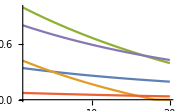

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.85|>];SizePlot[SimulateLawOfMotion[RandomPowerStructure[5]]]
```

### Animation

#### GenerateReel

Generates a sequence of power structure graph plots (a “reel”) from a simulation. Output: list of graph plots.

```mathematica
GenerateReel[simulation_List]:=Map[ShowPowerStructure,simulation]
```

Same as above, but accepts options for ShowPowerStructure.

```mathematica
GenerateReel[simulation_List,options_Association]:=Map[ShowPowerStructure[#,options]&,simulation]
```

#### ExportSimulationAsGIF

Export an animated simulation to a .gif file (the file name must end in .gif). Output: none.

```mathematica
ExportSimulationAsGIF[simulation_List,file_String]:= Export[file,GenerateReel[simulation],"DisplayDurations"->1,"AnimationRepetitions"->Infinity]
```

```mathematica
ExportSimulationAsGIF[simulation_List,file_String,options_Association]:= Export[file,GenerateReel[simulation,options],"DisplayDurations"->1,"AnimationRepetitions"->Infinity]
```

```mathematica
ExportSimulationAsGIF[SimulateLawOfMotion[ps],"/Users/..."];
```

### Move Sequences and Distributions

#### ShowMoveSequence

```mathematica
ShowMoveSequence[a_Association]:=SpacedRow[MapIndexed[AddCaption[
Tooltip[ShowPowerStructure[#[[2]],<|"focal"->First[#],"circular"->True|>],Pretty[#[[2]]]],"t="<>ToString[First[#2]-1]]&,Transpose[{a["seq"],a["sim"]}]],15]
```

```mathematica
ShowMoveSequence[a_Association]:=SpacedRow[MapIndexed[AddCaption[
Tooltip[ShowPowerStructure[#[[2]],<|"focal"->First[#]|>],Round[#[[2]]["s"],.01]],"t="<>ToString[First[#2]-1]]&,Transpose[{a["seq"],a["sim"]}]],15]
```

```mathematica
ShowMoveSequence[a]
```

-Graphics-
t=0-Graphics-
t=1-Graphics-
t=2

#### SimClip

Extract a subsequence from a move sequence. Output: Association.

```mathematica
SimClip[sim_,start_,end_]:=<|
"sim"->Take[sim["sim"],{start+1,end+1}],"seq"->Join[{0},Take[sim["seq"],{start+2,end+1}]],
"plies"->sim["plies"],
"b"->sim["b"],
"params"->sim["params"]
|>
```

#### ShowMoveDistribution

Given a power structure and a moving agent, return the statistical distribution of the agent’s best moves over all possible move permutations up to a given depth (plies). Output: an Association listing power structures and their percentages.

```mathematica
ShowMoveDistribution[ps_,i_,plies_,b_]:=Block[{orders=Map[Join[{i},#]&,Tuples[Range[Length[ps["s"]]],plies-1]]},
Map[Round[#/Length[orders],.01]&,ReverseSort[Counts[Map[ShowPowerStructure[Minimax[ps,#,b]["Move"],<|"circular"->True,"focal"->i|>]&,orders]]]]
]
```

```mathematica
SetParameters[<|"β"->2,"μ"->5,"λ"->.995,"α"->2.25,"δ"->0.8, "ρ"->0.98,"k"->9,"Δ"->0.05|>];ps=PowerStructure[{1,.8,.8},NamedTHierarchy[3]];
ShowPowerStructure[ps,<|"circular"->True|>]
ShowMoveDistribution[ps,1,5,6]//AbsoluteTiming
```

-Graphics-

{16.5005,<|-Graphics-→0.63,-Graphics-→0.14,-Graphics-→0.14,-Graphics-→0.05,-Graphics-→0.05|>}

#### ShowWeightedMoveDistribution

Given a power structure and a moving agent, return the statistical distribution of the agent’s randomly-weighted moves of a given depth (plies). Output: an Association listing power structures and their percentages.

```mathematica
ShowWeightedMoveDistribution[ps_,i_,plies_,b_,samples_]:=
Map[Round[#/samples,.01]&,ReverseSort[Counts[Table[ShowPowerStructure[WeightedMove[ps,i,plies,b],<|"circular"->True,"focal"->i|>],samples]]]]
```

```mathematica
SetParameters[<|"β"->2,"μ"->5,"λ"->.995,"α"->2.25,"δ"->0.8, "ρ"->0.98,"k"->9,"Δ"->0.05|>];ps=PowerStructure[{1,.8,.8},NamedTHierarchy[3]];
ShowPowerStructure[ps,<|"circular"->True|>]
ShowWeightedMoveDistribution[ps,1,3,5,20]//AbsoluteTiming
```

-Graphics-

{0.641006,<|-Graphics-→0.55,-Graphics-→0.25,-Graphics-→0.2|>}

## Unit Tests

### Tests

Master unit test report:

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25, "k"->29|>];report=TestReport[Catenate[{

(* Tactics *)
unitTests["RandomS"],
unitTests["LegalTacticQ"],
unitTests["LegalTacticQ"],
unitTests["LegalTQ"],
unitTests["RandomTactic"],
unitTests["RandomTacticMatrix"],
unitTests["TernaryMatrixQ"],
unitTests["NormalizeS"],
unitTests["NormalizeTactic"],
unitTests["NormalizeTernaryT"],
unitTests["ToTernary"],
unitTests["SetTactic"],

(* Simulation Engine *)
unitTests["UpdateS"],
unitTests["SimulateLawOfMotion"],
unitTests["Utility"],
unitTests["PrinceRank"],

(* Visualization *)
unitTests["ShowPowerStructure"],

(* Helper Functions *)
unitTests["HelperFunctions"]
}]]
```

TestReportObject[…]

### Analyzing Failures

Shows which test cases failed:

```mathematica
report["TestsFailedWrongResults"]
```

<||>